#### Notebook Description

This notebook is for brain storming.

#### Project Goals

Construct a symbolic representation of a chessboard state (ChessState) and chess moves (ChessMove) in the Wolfram Language.
Develop a function which takes a ChessState and a ChessPlay and returns the new ChessState.
Build a ConvertChessNotation function for converting between the Wolfram and the algebraic chess notation.
Curate a Chess Dataset of famous chess games in the history for the data repository.
Create a ChessStatePlot function which plots a given ChessState on a chessboard. 
Create a ChessMovePlot function that plots the transition from the inputted ChessState to the next state specified by a ChessMove, alongside with a ChessAnimate function that animates a chess game (a dataset or a list of ChessMove’s).
Depending on the amount of remaining time, write a ListGameMove function that receives a ChessState (and ChessRules) and outputs all the possible ChessMove’s. 
Potentially, provide Evaluate → True/”Best” option for ListChessMove which returns sorted and associate predicted winning probabilities/scores for white using an external game engine.
Note: This project will be done keeping in mind that eventually the word Chess in the above functions would be replaced by the word Game, generalizing to as many board and card games possible.

### Chess Pieces

#### Chess Piece Names

```mathematica
If[
	NotebookDirectory[] ≠ ""
	, 
	packageDir = NotebookDirectory[];
	,
	packageDir = $InputFileName;
]
packageDir
```

/home/miladiouss/MiladBox/Mathematica/WSS18/Summer2018Starter/ChessPackage/

```mathematica
pieceNamesShort = {"King", "Queen", "Rook", "Bishop", "Knight", "Pawn"};
wpn = Table["White" <> pieceName, {pieceName, pieceNamesShort}];
bpn = Table["Black" <> pieceName, {pieceName, pieceNamesShort}];
pieceNames = wpn ~Join~ bpn;
AppendTo[pieceNames, "EmptySquare"];
```

```mathematica
pieceSymbols = 
	{"♔", "♕", "♖", "♗", "♘", "♙"} ~Join~
	{"♚", "♛", "♜", "♝", "♞", "♟"} ~Join~
	{"□"};
```

```mathematica
{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □} = pieceSymbols;
(*{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □} = pieceNames;*)
```

#### Download/Load Chess Piece Images

```mathematica
If[
	FileExistsQ[packageDir <> "pieceImages.mx"]
	,
	pieceImages = Import[NotebookDirectory[] <> "pieceImages.mx"];
	Print["Chess piece images were loaded."];
	,
	piecePicLinksWiki =
		{
		"https://upload.wikimedia.org/wikipedia/commons/thumb/4/42/Chess_klt45.svg/75px-Chess_klt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/1/15/Chess_qlt45.svg/75px-Chess_qlt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/7/72/Chess_rlt45.svg/75px-Chess_rlt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/b/b1/Chess_blt45.svg/75px-Chess_blt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/7/70/Chess_nlt45.svg/75px-Chess_nlt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/4/45/Chess_plt45.svg/75px-Chess_plt45.svg.png"
		} ~Join~
		{
		"https://upload.wikimedia.org/wikipedia/commons/thumb/f/f0/Chess_kdt45.svg/75px-Chess_kdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/4/47/Chess_qdt45.svg/75px-Chess_qdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/f/ff/Chess_rdt45.svg/75px-Chess_rdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/9/98/Chess_bdt45.svg/75px-Chess_bdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/e/ef/Chess_ndt45.svg/75px-Chess_ndt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/c/c7/Chess_pdt45.svg/75px-Chess_pdt45.svg.png"
		};

	imagePicMotherLink = "https://marcelk.net/chess/pieces/merida/320/";
	piecePicLinks = Table["https://marcelk.net/chess/pieces/merida/320/" <> pieceName <> ".png", {pieceName, Most @ pieceNames}];

	pieceImages = 
		Import /@ piecePicLinks;
	AppendTo[pieceImages, Graphics[{Hue[0, 0, 1, 0], Rectangle[]}, ImageSize -> ImageDimensions @ First @ pieceImages]];
	Export[NotebookDirectory[]<>"pieceImages.mx",pieceImages];
	Print["Chess piece images were downloaded."];
]
```

Chess piece images were loaded.

#### Chess Piece Object

```mathematica
pieceObj = 
	MapThread[
		#1 -> <|"Name" -> #2, "Symbol" -> #3, "Image" -> #4|>&,
		{pieceSymbols, pieceNames, pieceSymbols, pieceImages}
	];
	
pieceObj = Association @ pieceObj;
```

Example of using pieceObj

```mathematica
ImageResize[pieceObj[♔]["Image"],50]
pieceObj[♔]["Symbol"]
```

-Graphics-

♔

### Setups

#### Setup Initial Chess State

```mathematica
coords = ({{"a8", "b8", "c8", "d8", "e8", "f8", "g8", "h8"}, {"a7", "b7", "c7", "d7", "e7", "f7", "g7", "h7"}, {"a6", "b6", "c6", "d6", "e6", "f6", "g6", "h6"}, {"a5", "b5", "c5", "d5", "e5", "f5", "g5", "h5"}, {"a4", "b4", "c4", "d4", "e4", "f4", "g4", "h4"}, {"a3", "b3", "c3", "d3", "e3", "f3", "g3", "h3"}, {"a2", "b2", "c2", "d2", "e2", "f2", "g2", "h2"}, {"a1", "b1", "c1", "d1", "e1", "f1", "g1", "h1"}});
stateNameArray = ({{♜, ♞, ♝, ♛, ♚, ♝, ♞, ♜}, {♟, ♟, ♟, ♟, ♟, ♟, ♟, ♟}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {♙, ♙, ♙, ♙, ♙, ♙, ♙, ♙}, {♖, ♘, ♗, ♕, ♔, ♗, ♘, ♖}});
state0 = AssociationThread[Flatten[coords] -> Flatten[stateNameArray]];
AssociateTo[state0, "WhiteCemetery" -> {}];
AssociateTo[state0, "BlackCemetery" -> {}];
state  = state0;
```

Example of extracting information from state

```mathematica
state["a1"]
```

♖

### ChessPlot

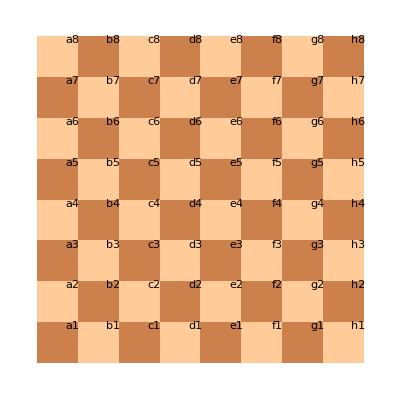

-Graphics-

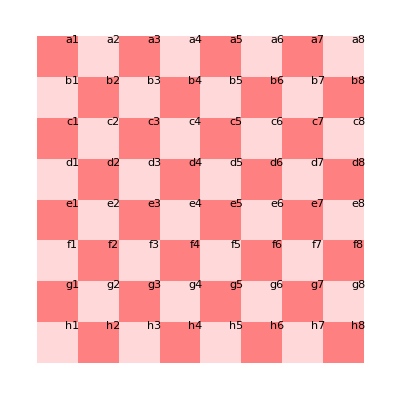

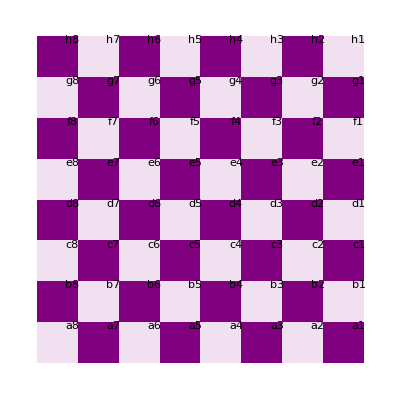

```mathematica
files = {"a", "b", "c", "d", "e", "f", "g", "h"};
ranks = {"1", "2", "3", "4", "5", "6", "7", "8"};
		
emptyBoard = Table[Mod[i + j, 2], {i, 8}, {j, 8}];
		
tabulatePieceInset[insetToAlgFunc_, state_] :=
	Table[
		Inset[
			pieceObj[state[insetToAlgFunc[i, j]]]["Image"], 
			{i, j} - {1, 1}, 
			{i, j} - {1, 1}, 
			1
		]
		,
		{i, 8}
		, 
		{j, 8}
	];
			
tabulateCoordInset[insetToAlgFunc_] := 
	Table[
		Inset[
			Text[Style[insetToAlgFunc[i, j], 7]], 
			{i, j} + {-0.12, -0.09},
			Automatic,
			1
		]
		,
		{i, 8}
		,
		{j, 8}
	];
		

(* White -> Down, Origin is a1 *)
whiteDownCoordTable = 
	tabulateCoordInset[{i, j} ↦ files⟦i⟧ <> ranks⟦j⟧];
(* White -> Up, Origin is h8 *)
whiteUpCoordTable = 
	tabulateCoordInset[{i, j} ↦ files⟦9 - i⟧ <> ranks⟦9 - j⟧];
(* White -> Left, Origin is h1 *)
whiteLeftCoordTable = 
	tabulateCoordInset[{i, j} ↦ files⟦9 - j⟧ <> ranks⟦i⟧];
(* White -> right, Origin is a8 *)
whiteRightCoordTable =
	tabulateCoordInset[{i, j} ↦ files⟦j⟧ <> ranks⟦9 - i⟧];

bottomLeftBlackBoard = Table[Mod[i + j    , 2], {i, 8}, {j, 8}];
bottomLeftWhiteBoard = Table[Mod[i + j + 1, 2], {i, 8}, {j, 8}];
		
Options[ChessPlot] = Join[
	{"WhiteOrientation" -> Automatic, "BoardColorSet" -> Automatic, "ShowCoordinates" -> True},
	Options[ArrayPlot]
];
ChessPlot[ChessState_, opts: OptionsPattern[]] :=
	
	Module[{state = ChessState},

		(* Board Orientation *)
		Switch[
			OptionValue["WhiteOrientation"],
			Automatic | "Down",
				pieceInset = tabulatePieceInset[{i, j} ↦ files⟦i⟧ <> ranks⟦j⟧, state];
				coordInset = whiteDownCoordTable;
				emptyBoard = bottomLeftBlackBoard;
			,
			"Up",
				pieceInset = tabulatePieceInset[{i, j} ↦ files⟦9 - i⟧ <> ranks⟦9 - j⟧, state];
				coordInset = whiteUpCoordTable;
				emptyBoard = bottomLeftBlackBoard;
			,
			"Left",
				pieceInset = tabulatePieceInset[{i, j} ↦ files⟦9 - j⟧ <> ranks⟦i⟧, state];
				coordInset = whiteLeftCoordTable;
				emptyBoard = bottomLeftWhiteBoard;
			,
			"Right",
				pieceInset = tabulatePieceInset[{i, j} ↦ files⟦j⟧ <> ranks⟦9 - i⟧, state];
				coordInset = whiteRightCoordTable;
				emptyBoard = bottomLeftWhiteBoard;
			,
			_,
				Message["Wrong \"WhiteOrientation\" option was provided. Try \"Up\" for instance."]; Return[$Failed];
		];
		
		(* Board Color *)
		Switch[
			OptionValue["BoardColorSet"],
			Automatic,
				LightSquareColor = RGBColor[1.0, 0.8, 0.6];
				DarkSquareColor = RGBColor[0.8, 0.5, 0.3];
			,
			{_?ColorQ, _?ColorQ},
				{LightSquareColor, DarkSquareColor} = OptionValue["BoardColorSet"];
			,
			_,
				Message["Wrong \"BoardColorSet\" Sepcified. Try {White, Gray} for instance."]; Return[$Failed];
		];
		
		Switch[
			OptionValue["ShowCoordinates"],
			True,
				insetList = pieceInset ~Join~ coordInset;
			,
			False,
				insetList = pieceInset ~Join~ {};
			,
			_,
				Message["\"ShowCoordinates\" can either be True or False."]; Return[$Failed];
		];

		plot = 		
			ArrayPlot[
				emptyBoard,
				ColorRules -> {0 -> LightSquareColor, 1 -> DarkSquareColor}, 
				Epilog -> insetList,
				FilterRules[{opts}, Options[ArrayPlot]]
			];
		
		plot
	]

ChessPlot[state]
ChessPlot[state, "WhiteOrientation" -> "Up",    "BoardColorSet" -> {White, Darker@Gray}, "ShowCoordinates" -> False, ImageSize -> 100]
ChessPlot[state, "WhiteOrientation" -> "Left",  "BoardColorSet" -> {LightRed, Pink}]
ChessPlot[state, "WhiteOrientation" -> "Right", "BoardColorSet" -> {LightPurple, Purple}]
```

```mathematica
"♔"
```

♔

```mathematica
ClearAll[tabulatePieceInset]
```

You can double check orientation using the following image:

```mathematica
img=-Graphics-;
ImageRotate[img,-180°];
```

### ChessMove

```mathematica
chessMove[[1]]
```

b8

```mathematica
"□"//FullForm
```

"\[EmptySquare]"

```mathematica
{♛}∈{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □}
```

{♛}∈{♔,♕,♖,♗,♘,♙,♚,♛,♜,♝,♞,♟,□}

```mathematica
MemberQ[{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □},♛]
```

True

```mathematica
ChessPlay[ChessState_, ChessMove_] := 
	Module[{state = ChessState, chessMove = ChessMove},
			square1 = chessMove⟦1⟧;
			square2 = chessMove⟦2⟧;
			piece1  = state[chessMove⟦1⟧];
			piece2  = state[chessMove⟦2⟧];
			
			If[MemberQ[{♔, ♕, ♖, ♗, ♘, ♙}, piece2], AppendTo[state["WhiteCemetery"], piece2]];
			If[MemberQ[{♚, ♛, ♜, ♝, ♞, ♟}, piece2], AppendTo[state["BlackCemetery"], piece2]];
		
			state[square2] = piece1;
			state[square1] = □;
			
			state
	]
```

```mathematica
state1 = ChessPlay[state1, "e5" -> "e1"];
ChessPlot[state1]
state1
```

-Graphics-

<|a8→♜,b8→□,c8→♝,d8→♛,e8→♚,f8→♝,g8→♞,h8→♜,a7→♟,b7→♟,c7→♟,d7→♟,e7→♟,f7→♟,g7→♟,h7→♟,a6→□,b6→□,c6→□,d6→□,e6→□,f6→□,g6→□,h6→□,a5→□,b5→□,c5→□,d5→□,e5→□,f5→□,g5→□,h5→□,a4→□,b4→□,c4→□,d4→□,e4→□,f4→□,g4→□,h4→□,a3→□,b3→□,c3→□,d3→□,e3→□,f3→□,g3→□,h3→□,a2→♙,b2→♙,c2→♙,d2→□,e2→♙,f2→♙,g2→♙,h2→♙,a1→♖,b1→♘,c1→♗,d1→♕,e1→♞,f1→♗,g1→♘,h1→♖,WhiteCemetery→{♙,♔},BlackCemetery→{}|>

{♔,♕,♖,♗,♘,♙,♚,♛,♜,♝,♞,♟,□}

### ChessState Object

```mathematica
MatrixForm@Partition[Normal@state[[;;-3]],8]
```

(a8→♜ | b8→♞ | c8→♝ | d8→♛ | e8→♚ | f8→♝ | g8→♞ | h8→♜
a7→♟ | b7→♟ | c7→♟ | d7→♟ | e7→♟ | f7→♟ | g7→♟ | h7→♟
a6→□ | b6→□ | c6→□ | d6→□ | e6→□ | f6→□ | g6→□ | h6→□
a5→□ | b5→□ | c5→□ | d5→□ | e5→□ | f5→□ | g5→□ | h5→□
a4→□ | b4→□ | c4→□ | d4→□ | e4→□ | f4→□ | g4→□ | h4→□
a3→□ | b3→□ | c3→□ | d3→□ | e3→□ | f3→□ | g3→□ | h3→□
a2→♙ | b2→♙ | c2→♙ | d2→♙ | e2→♙ | f2→♙ | g2→♙ | h2→♙
a1→♖ | b1→♘ | c1→♗ | d1→♕ | e1→♔ | f1→♗ | g1→♘ | h1→♖)

```mathematica
$piecesPattern = Alternatives @@ Most[pieceSymbols]
```

♔|♕|♖|♗|♘|♙|♚|♛|♜|♝|♞|♟

```mathematica
test[x_,y_,z_]:={x,y,z};
test[1,2,3][[1]]
```

1

```mathematica
ChessState[a_,b_]:=Association[a-> b]
```

```mathematica
ChessState[1,"a"]
```

<|1→a|>

```mathematica
StringMatchQ["g0", files ~~ ranks]
```

False

```mathematica
$piecesPattern = Alternatives @@ Most[pieceSymbols];
ChessState[a : {__Rule}] := ChessState[Association[a]] 
ChessState[a_?AssociationQ][pos_?StringQ] /; StringMatchQ[pos, files ~~ ranks] := Lookup[a, pos, □]
cs_ChessState[x_?StringQ, y_?StringQ] := cs[x <> y]
cs_ChessState[x_?IntegerQ, y_?IntegerQ] := cs[files[[x]], ToString[y]]
cs_ChessState[s_?StringQ] /; StringMatchQ[s, $piecesPattern] := 
	Replace[
		Position[First[cs], s],
		{
			{} -> {},
			any_ :> any[[All, 1, 1]]
		}
	]
cs_ChessState["ChessPlot", opts___] := ChessPlot[First[cs], opts]
ChessState /: MakeBoxes[cs_ChessState, StandardForm] := 
	InterpretationBox @@ 
		{
			RowBox[{"ChessState[", ToBoxes@ArrayPlot@emptyBoard, "]"}],
			cs
		}
```

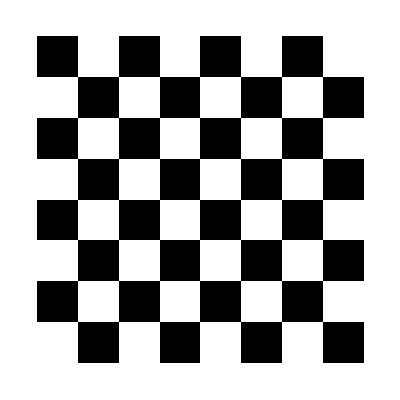
ChessState[-Graphics-]

```mathematica
cs =ChessState[state]
```

```mathematica
ToBoxes[cs["ChessPlot"]]
```

GraphicsBox[RasterBox[{{{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6}},{{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3}},{{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6}},{{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3}},{{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6}},{{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3}},{{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6}},{{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3},{1.,0.8,0.6},{0.8,0.5,0.3}}},{{0,0},{8,8}},{0,1}],Epilog→{{InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{0,0},{0,0},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{0,1},{0,1},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"a3"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{0,2},{0,2},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"a4"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{0,3},{0,3},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"a5"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{0,4},{0,4},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"a6"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{0,5},{0,5},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,255},ColorFunction→GrayLevel],BoxForm`ImageTag[Byte,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{0,6},{0,6},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{0,7},{0,7},1]},{InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{1,0},{1,0},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{1,1},{1,1},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"b3"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{1,2},{1,2},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"b4"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{1,3},{1,3},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"b5"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{1,4},{1,4},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"b6"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{1,5},{1,5},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,255},ColorFunction→GrayLevel],BoxForm`ImageTag[Byte,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{1,6},{1,6},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{1,7},{1,7},1]},{InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{2,0},{2,0},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{2,1},{2,1},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"c3"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{2,2},{2,2},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"c4"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{2,3},{2,3},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"c5"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{2,4},{2,4},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"c6"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{2,5},{2,5},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,255},ColorFunction→GrayLevel],BoxForm`ImageTag[Byte,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{2,6},{2,6},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{2,7},{2,7},1]},{InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{3,0},{3,0},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{3,1},{3,1},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"d3"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{3,2},{3,2},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"d4"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{3,3},{3,3},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"d5"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{3,4},{3,4},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"d6"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{3,5},{3,5},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,255},ColorFunction→GrayLevel],BoxForm`ImageTag[Byte,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{3,6},{3,6},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{3,7},{3,7},1]},{InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{4,0},{4,0},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{4,1},{4,1},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"e3"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{4,2},{4,2},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"e4"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{4,3},{4,3},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"e5"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{4,4},{4,4},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"e6"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{4,5},{4,5},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,255},ColorFunction→GrayLevel],BoxForm`ImageTag[Byte,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{4,6},{4,6},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{4,7},{4,7},1]},{InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{5,0},{5,0},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{5,1},{5,1},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"f3"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{5,2},{5,2},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"f4"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{5,3},{5,3},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"f5"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{5,4},{5,4},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"f6"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{5,5},{5,5},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,255},ColorFunction→GrayLevel],BoxForm`ImageTag[Byte,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{5,6},{5,6},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{5,7},{5,7},1]},{InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{6,0},{6,0},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{6,1},{6,1},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"g3"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{6,2},{6,2},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"g4"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{6,3},{6,3},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"g5"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{6,4},{6,4},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"g6"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{6,5},{6,5},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,255},ColorFunction→GrayLevel],BoxForm`ImageTag[Byte,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{6,6},{6,6},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{6,7},{6,7},1]},{InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{7,0},{7,0},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{7,1},{7,1},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"h3"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{7,2},{7,2},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"h4"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{7,3},{7,3},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"h5"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{7,4},{7,4},1],InsetBox[BoxData[FormBox[RowBox[{RowBox[{Missing,[,RowBox[{"KeyAbsent",,,RowBox[{Missing,[,RowBox[{"KeyAbsent",,,"h6"}],]}]}],]}],[,"Image",]}],TraditionalForm]],{7,5},{7,5},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,255},ColorFunction→GrayLevel],BoxForm`ImageTag[Byte,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{7,6},{7,6},1],InsetBox[BoxData[FormBox[GraphicsBox[TagBox[RasterBox[RawArray[…],{{0,320},{320,0}},{0,65535},ColorFunction→GrayLevel],BoxForm`ImageTag[Bit16,ColorSpace→Grayscale,Interleaving→True],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{320,320},PlotRange→{{0,320},{0,320}}],TraditionalForm]],{7,7},{7,7},1]},{InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["a1",7,StripOnInput→False],TextForm]],InlineText],a1],TraditionalForm]],{0.88,0.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["a2",7,StripOnInput→False],TextForm]],InlineText],a2],TraditionalForm]],{0.88,1.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["a3",7,StripOnInput→False],TextForm]],InlineText],a3],TraditionalForm]],{0.88,2.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["a4",7,StripOnInput→False],TextForm]],InlineText],a4],TraditionalForm]],{0.88,3.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["a5",7,StripOnInput→False],TextForm]],InlineText],a5],TraditionalForm]],{0.88,4.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["a6",7,StripOnInput→False],TextForm]],InlineText],a6],TraditionalForm]],{0.88,5.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["a7",7,StripOnInput→False],TextForm]],InlineText],a7],TraditionalForm]],{0.88,6.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["a8",7,StripOnInput→False],TextForm]],InlineText],a8],TraditionalForm]],{0.88,7.91},Automatic,1]},{InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["b1",7,StripOnInput→False],TextForm]],InlineText],b1],TraditionalForm]],{1.88,0.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["b2",7,StripOnInput→False],TextForm]],InlineText],b2],TraditionalForm]],{1.88,1.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["b3",7,StripOnInput→False],TextForm]],InlineText],b3],TraditionalForm]],{1.88,2.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["b4",7,StripOnInput→False],TextForm]],InlineText],b4],TraditionalForm]],{1.88,3.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["b5",7,StripOnInput→False],TextForm]],InlineText],b5],TraditionalForm]],{1.88,4.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["b6",7,StripOnInput→False],TextForm]],InlineText],b6],TraditionalForm]],{1.88,5.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["b7",7,StripOnInput→False],TextForm]],InlineText],b7],TraditionalForm]],{1.88,6.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["b8",7,StripOnInput→False],TextForm]],InlineText],b8],TraditionalForm]],{1.88,7.91},Automatic,1]},{InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["c1",7,StripOnInput→False],TextForm]],InlineText],c1],TraditionalForm]],{2.88,0.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["c2",7,StripOnInput→False],TextForm]],InlineText],c2],TraditionalForm]],{2.88,1.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["c3",7,StripOnInput→False],TextForm]],InlineText],c3],TraditionalForm]],{2.88,2.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["c4",7,StripOnInput→False],TextForm]],InlineText],c4],TraditionalForm]],{2.88,3.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["c5",7,StripOnInput→False],TextForm]],InlineText],c5],TraditionalForm]],{2.88,4.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["c6",7,StripOnInput→False],TextForm]],InlineText],c6],TraditionalForm]],{2.88,5.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["c7",7,StripOnInput→False],TextForm]],InlineText],c7],TraditionalForm]],{2.88,6.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["c8",7,StripOnInput→False],TextForm]],InlineText],c8],TraditionalForm]],{2.88,7.91},Automatic,1]},{InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["d1",7,StripOnInput→False],TextForm]],InlineText],d1],TraditionalForm]],{3.88,0.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["d2",7,StripOnInput→False],TextForm]],InlineText],d2],TraditionalForm]],{3.88,1.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["d3",7,StripOnInput→False],TextForm]],InlineText],d3],TraditionalForm]],{3.88,2.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["d4",7,StripOnInput→False],TextForm]],InlineText],d4],TraditionalForm]],{3.88,3.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["d5",7,StripOnInput→False],TextForm]],InlineText],d5],TraditionalForm]],{3.88,4.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["d6",7,StripOnInput→False],TextForm]],InlineText],d6],TraditionalForm]],{3.88,5.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["d7",7,StripOnInput→False],TextForm]],InlineText],d7],TraditionalForm]],{3.88,6.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["d8",7,StripOnInput→False],TextForm]],InlineText],d8],TraditionalForm]],{3.88,7.91},Automatic,1]},{InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["e1",7,StripOnInput→False],TextForm]],InlineText],e1],TraditionalForm]],{4.88,0.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["e2",7,StripOnInput→False],TextForm]],InlineText],e2],TraditionalForm]],{4.88,1.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["e3",7,StripOnInput→False],TextForm]],InlineText],e3],TraditionalForm]],{4.88,2.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["e4",7,StripOnInput→False],TextForm]],InlineText],e4],TraditionalForm]],{4.88,3.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["e5",7,StripOnInput→False],TextForm]],InlineText],e5],TraditionalForm]],{4.88,4.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["e6",7,StripOnInput→False],TextForm]],InlineText],e6],TraditionalForm]],{4.88,5.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["e7",7,StripOnInput→False],TextForm]],InlineText],e7],TraditionalForm]],{4.88,6.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["e8",7,StripOnInput→False],TextForm]],InlineText],e8],TraditionalForm]],{4.88,7.91},Automatic,1]},{InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["f1",7,StripOnInput→False],TextForm]],InlineText],f1],TraditionalForm]],{5.88,0.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["f2",7,StripOnInput→False],TextForm]],InlineText],f2],TraditionalForm]],{5.88,1.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["f3",7,StripOnInput→False],TextForm]],InlineText],f3],TraditionalForm]],{5.88,2.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["f4",7,StripOnInput→False],TextForm]],InlineText],f4],TraditionalForm]],{5.88,3.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["f5",7,StripOnInput→False],TextForm]],InlineText],f5],TraditionalForm]],{5.88,4.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["f6",7,StripOnInput→False],TextForm]],InlineText],f6],TraditionalForm]],{5.88,5.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["f7",7,StripOnInput→False],TextForm]],InlineText],f7],TraditionalForm]],{5.88,6.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["f8",7,StripOnInput→False],TextForm]],InlineText],f8],TraditionalForm]],{5.88,7.91},Automatic,1]},{InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["g1",7,StripOnInput→False],TextForm]],InlineText],g1],TraditionalForm]],{6.88,0.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["g2",7,StripOnInput→False],TextForm]],InlineText],g2],TraditionalForm]],{6.88,1.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["g3",7,StripOnInput→False],TextForm]],InlineText],g3],TraditionalForm]],{6.88,2.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["g4",7,StripOnInput→False],TextForm]],InlineText],g4],TraditionalForm]],{6.88,3.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["g5",7,StripOnInput→False],TextForm]],InlineText],g5],TraditionalForm]],{6.88,4.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["g6",7,StripOnInput→False],TextForm]],InlineText],g6],TraditionalForm]],{6.88,5.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["g7",7,StripOnInput→False],TextForm]],InlineText],g7],TraditionalForm]],{6.88,6.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["g8",7,StripOnInput→False],TextForm]],InlineText],g8],TraditionalForm]],{6.88,7.91},Automatic,1]},{InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["h1",7,StripOnInput→False],TextForm]],InlineText],h1],TraditionalForm]],{7.88,0.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["h2",7,StripOnInput→False],TextForm]],InlineText],h2],TraditionalForm]],{7.88,1.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["h3",7,StripOnInput→False],TextForm]],InlineText],h3],TraditionalForm]],{7.88,2.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["h4",7,StripOnInput→False],TextForm]],InlineText],h4],TraditionalForm]],{7.88,3.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["h5",7,StripOnInput→False],TextForm]],InlineText],h5],TraditionalForm]],{7.88,4.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["h6",7,StripOnInput→False],TextForm]],InlineText],h6],TraditionalForm]],{7.88,5.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["h7",7,StripOnInput→False],TextForm]],InlineText],h7],TraditionalForm]],{7.88,6.91},Automatic,1],InsetBox[BoxData[FormBox[InterpretationBox[Cell[BoxData[FormBox[StyleBox["h8",7,StripOnInput→False],TextForm]],InlineText],h8],TraditionalForm]],{7.88,7.91},Automatic,1]}},Frame→Automatic,FrameLabel→{None,None},FrameTicks→{{None,None},{None,None}},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],Method→{DefaultBoundaryStyle→Automatic,DefaultPlotStyle→Automatic}]

### Game PGN

```mathematica
gameString = "1. e4 e5 2. Nf3 Nc6 3. Nc3 Nf6 4. Bb5 Bb4 5. O-O O-O 6. d3 Bxc3 7. bxc3 d6 8.
Bg5 Bd7 9. Nd2 h6 10. Bh4 g5 11. Bg3 Ne7 12. Bxd7 Nxd7 13. d4 f5 14. exf5 exd4
15. cxd4 Nxf5 16. Qf3 Rf7 17. Qxb7 Nxd4 18. Qe4 Nf5 19. Rae1 Qc8 20. f4 Nf6 21.
Qd3 g4 22. Bf2 Qd7 23. Bd4 Nxd4 24. Qxd4 Qb5 25. Kh1 Qd5 26. Qf2 Qxa2 27. Nb3 a5
28. Ra1 Qb2 29. Nxa5 Qc3 30. Nb3 Rxa1 31. Nxa1 Nd5 32. g3 Re7 33. Nb3 Re3 34.
Rd1 Nf6 35. Nd2 Qxc2 36. Qxe3 Qxd1+ 37. Kg2 Kf7 38. f5 Qa1 39. Qxh6 Qd4 40. Qg6+
Ke7 41. Qg7+ Ke8 42. Qg5 Qd5+ 43. Kg1 Kf7 44. Qg6+ Ke7 45. Qg7+ Qf7 46. Qg5 Qd5
47. Qg7+ Qf7 48. Qg5 Qd5 49. Qg7+ 1/2-1/2";

(* Remove newline *)
gameString = StringReplace[gameString,{"\n" -> " "}];

(* Remove game result *)
gameResultStrings = {"1-0", "0-1", "1/2-1/2"};
gameString = StringSplit[gameString, gameResultStrings]⟦1⟧;

(* Splite to turns *)
gs = StringSplit[gameString, DigitCharacter..~~"."];

(* Splite to moves *)
gs = StringSplit[#,WhitespaceCharacter]&/@ gs;
TableView[gs]
```

e4e5Nf3Nc6Nc3Nf6Bb5Bb4O-OO-Od3Bxc3bxc3d6Bg5Bd7Nd2h6Bh4g5Bg3Ne7Bxd7Nxd7d4f5exf5exd4cxd4Nxf5Qf3Rf7Qxb7Nxd4Qe4Nf5Rae1Qc8f4Nf6Qd3g4Bf2Qd7Bd4Nxd4Qxd4Qb5Kh1Qd5Qf2Qxa2Nb3a5Ra1Qb2Nxa5Qc3Nb3Rxa1Nxa1Nd5g3Re7Nb3Re3Rd1Nf6Nd2Qxc2Qxe3Qxd1+Kg2Kf7f5Qa1Qxh6Qd4Qg6+Ke7Qg7+Ke8Qg5Qd5+Kg1Kf7Qg6+Ke7Qg7+Qf7Qg5Qd5Qg7+Qf7Qg5Qd5Qg7+

```mathematica
Map[Association@Thread[If[Length[#]==2,{"White","Black"},{"White"}]->#]&,gs]
```

{<|White→e4,Black→e5|>,<|White→Nf3,Black→Nc6|>,<|White→Nc3,Black→Nf6|>,<|White→Bb5,Black→Bb4|>,<|White→O-O,Black→O-O|>,<|White→d3,Black→Bxc3|>,<|White→bxc3,Black→d6|>,<|White→Bg5,Black→Bd7|>,<|White→Nd2,Black→h6|>,<|White→Bh4,Black→g5|>,<|White→Bg3,Black→Ne7|>,<|White→Bxd7,Black→Nxd7|>,<|White→d4,Black→f5|>,<|White→exf5,Black→exd4|>,<|White→cxd4,Black→Nxf5|>,<|White→Qf3,Black→Rf7|>,<|White→Qxb7,Black→Nxd4|>,<|White→Qe4,Black→Nf5|>,<|White→Rae1,Black→Qc8|>,<|White→f4,Black→Nf6|>,<|White→Qd3,Black→g4|>,<|White→Bf2,Black→Qd7|>,<|White→Bd4,Black→Nxd4|>,<|White→Qxd4,Black→Qb5|>,<|White→Kh1,Black→Qd5|>,<|White→Qf2,Black→Qxa2|>,<|White→Nb3,Black→a5|>,<|White→Ra1,Black→Qb2|>,<|White→Nxa5,Black→Qc3|>,<|White→Nb3,Black→Rxa1|>,<|White→Nxa1,Black→Nd5|>,<|White→g3,Black→Re7|>,<|White→Nb3,Black→Re3|>,<|White→Rd1,Black→Nf6|>,<|White→Nd2,Black→Qxc2|>,<|White→Qxe3,Black→Qxd1+|>,<|White→Kg2,Black→Kf7|>,<|White→f5,Black→Qa1|>,<|White→Qxh6,Black→Qd4|>,<|White→Qg6+,Black→Ke7|>,<|White→Qg7+,Black→Ke8|>,<|White→Qg5,Black→Qd5+|>,<|White→Kg1,Black→Kf7|>,<|White→Qg6+,Black→Ke7|>,<|White→Qg7+,Black→Qf7|>,<|White→Qg5,Black→Qd5|>,<|White→Qg7+,Black→Qf7|>,<|White→Qg5,Black→Qd5|>,<|White→Qg7+|>}

### Carlo’s Notes

```mathematica
ChessState[a_?AssociationQ][s_?StringQ] /; StringMatchQ[s, LetterCharacter~~DigitCharacter];
ChessState[state]["a1"];
```

Carlo’s Idea:

```mathematica
wki=pieceObj[♔]["Image"];
	bki=pieceObj[♚]["Image"];
	
	pi = {wki, bki};

	pPos = {{1,1},{2,3}};
	
	LocatorPane[
		Dynamic[pPos],
		ap,
		Appearance -> pi];
```